```mathematica
(* Computer Graphics with Applications of Dr. Makhanov (Google's Version) *)
```

```mathematica
(* Lecture 3. Pure functions. 3D Graphics: Parametric, Spherical and Revolution Surfaces; Space Curves. *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot, Graphics , Graphics3D,SphericalPlot3D,DensityPlot,DensityPlot3D,ContourPlot,SliceContourPlot3D,SliceDensityPlot3D,RegionPlot,RegionPlot3D,Graphics3D,RevolutionPlot3D},ImageSize->Medium];
```

```mathematica
(* The pure function with one parameter is shown below. # stands for the argument and & the end of the function's body  [x] - argument with the [] around. *)
(* (3+#)&
This defines a pure function (or anonymous function).
The # represents an argument (placeholder).
& marks the end of the function definition.
So,(3+#)& is a function that takes an input and adds 3 to it. *)
```

```mathematica
(3+#)&[x]
```

3+x

```mathematica
(3+#)&[7]
```

10

```mathematica
(* Define f3 using pure function syntax  *)
```

```mathematica
f3=3+#&
```

3+#1&

```mathematica
f3[8]
```

11

```mathematica
(* #1,#2,..#N - stand for the first, second and N-th argument *)
```

```mathematica
fs=#1+#2+#3& (* ahhhhh *)
```

#1+#2+#3&

```mathematica
fs[1,2,3]
```

6

```mathematica
(* fs[1,2,3,4] also works *)
```

```mathematica
fs[1,2, 3, 4] (* argument เกินมาก็ไม่เป็นไร แต่ถ้า less argument อันนั้นจะ error— that means >=3 is okay *)
```

6

```mathematica
(*Parametric circle defined directly inside the Plot by the pure function *)
```

```mathematica
R = 1
```

1

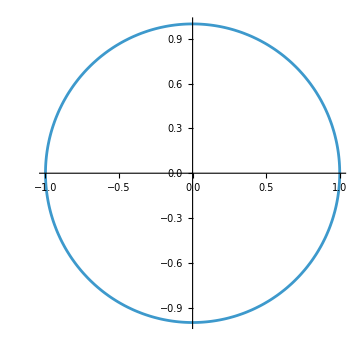

```mathematica
ParametricPlot[{R Cos[#1],R Sin[#1]}&[t],{t,0,2Pi}]
```

```mathematica
(* Extra arguments are ignored *)
```

```mathematica
fNP1=Sin[#1^2]&
```

Sin[#1^2]&

```mathematica
(* fNP1[x,y] works *)
```

```mathematica
fNP1[0.5,1]
```

0.247404

```mathematica
(* Define and plot a pure function  Sin[#1^2-#2]& *)
```

```mathematica
Clear[fP1]
```

```mathematica
fP1=Sin[#1^2-#2]&
```

Sin[#1^2-#2]&

```mathematica
fP1[x,y]
```

Sin[x^2-y]

```mathematica
Plot3D[fP1[x,y],{x,-2,2},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Define and plot f1:R2:=R3 f1E=Exp[Sin[#1*#2]] *)
```

```mathematica
(* An explicit surface f1E[x_,y_] *)
```

```mathematica
f1E[x_,y_]:=Exp[Sin[x y]]
```

```mathematica
Plot3D[f1E[x, y],{x,0,4},{y,0,4}]
```

-Graphics3D-

```mathematica
(* Pure function f1P *)
```

```mathematica
f1P:=Exp[Sin[#1 #2]]& (*อย่าลืม end of the body ก็คือ & ด้วย*)
```

```mathematica
Plot3D[f1P[x, y],{x,0,4},{y,0,4}]
```

-Graphics3D-

```mathematica
(* The Wolfram Language provides hundreds of options to control every aspect of the construction and styling of graphics. The options are carefully designed to be both flexible and powerful,and to fit in with the Wolfram Language's sophisticated built-in algorithms for aesthetic optimization*)
```

```mathematica
(*Example 0  *)
```

```mathematica
Plot3D[f1P[x, y],{x,0,4},{y,0,4},PlotPoints->40,Mesh->False,
BaseStyle->{"Helvetica",FontSize->12},AxesLabel->{"Length","Width","Height"},
FaceGrids->All,PlotStyle->{Glow[Red],Opacity[0.5]},ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* Self study: explore Options, remove ; check the options -F1 and experiment *)
```

```mathematica
Options[Plot3D];
```

```mathematica
(* Example 1 Parametric surface f:R2->R3 S1[u_,v_]:={x1[u,v],y1[u,v],z1[u,x]} *)
```

```mathematica
Clear[S1,R1,x1,y1,z1]
```

```mathematica
x1[u_,v_]:=u^2
```

```mathematica
y1[u_,v_]:=v^2
```

```mathematica
z1[u_,v_]:=0.01*Sin[u*v]
```

```mathematica
S1[u_,v_]:={x1[u,v],y1[u,v],z1[u,v]}
```

```mathematica
(* Call, graph *)
```

```mathematica
S1[2,3]
```

{4,9,-0.00279415}

```mathematica
(* Scale problem z-small,x,y -large *)
```

```mathematica
GSp=ParametricPlot3D[S1[u,v],{u,0,4},{v,0,4},PlotStyle->Blue, MeshStyle->White]
```

-Graphics3D-

```mathematica
GSp=ParametricPlot3D[S1[u,v],{u,0,4},{v,0,4},BoxRatios->{1,1,0.3},PlotStyle->Blue, MeshStyle->White]
```

-Graphics3D-

```mathematica
(* Screen coordinates, scale, discuss BoxRatios->{1,1,0.3} *)
```

```mathematica
(* As an example consider a pure function f:R2->R3 *)
```

```mathematica
S1p={#1^2,#2^2,0.01*Cos[#1*#2]}&
```

{#1^2,#2^2,0.01 Cos[#1 #2]}&

```mathematica
GSp1=ParametricPlot3D[S1p[u,v],{u,0,4},{v,0,4},BoxRatios->{1,1,0.3}]
```

-Graphics3D-

```mathematica
Show[{GSp,GSp1}]
```

-Graphics3D-

```mathematica
(* Example 2. Find intersections of Surface 1: Sin[x*y^2] and Surface 2  0.5*x*y {x,-2,2},{y,-2,2} *)
```

```mathematica
Clear[f1,f2,f3]
```

```mathematica
(* Surface 1 *)
```

```mathematica
f1[x_,y_]:=Sin[x*y^2]
```

```mathematica
(* Surface 2 *)
```

```mathematica
f2[x_,y_]:=0.5*x*y
```

```mathematica
(* Intersection shows the solution of the equations f1[x,y]-f2[x,y] = 0 *)
```

```mathematica
Plot3D[{f1[x,y],f2[x,y]},{x,-2,2},{y,-2,2} ,PlotStyle->{Yellow,Red}]
```

-Graphics3D-

```mathematica
(* Example 3. Experiment withtersections of Surface 1: Sin[x*y^2] and the parametric Surface 2 {u,v,u^3/3+u v^2+2 (u^2-v^2)}, {x,-2,2} {y,-2,2} {u,-1,1} {v-1,1} *)
```

```mathematica
Gf1=Plot3D[f1[x,y],{x,-2,2},{y,-2,2} ,PlotStyle->Yellow]
```

-Graphics3D-

```mathematica
f3[u_,v_]:={u,v,u^2/3+u v^2+2 (u^2-v^2)}
```

```mathematica
Gf3=ParametricPlot3D[f3[u,v],{u,-1,1},{v,-1,1},PlotStyle->Blue,MeshStyle->Yellow,BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[{Gf1,Gf3},ImageSize->Large]
```

-Graphics3D-

```mathematica
(* Space curve in 3D f:R1->R3 e.g.  f[t_]:={fx[t],fy[t],fz[t]} *)
```

```mathematica
(* Example 0 Spiral with the radius R in 3D (memorize) 
x[t_]:=R Cos[t]
y[t]:=R Sin[t] REMEMBER THIS!!!!!!
z[t]:=t
Spiral[t_]:={x[t],y[t],z[t]}
or the pure function  
{R Sin[#1],R Cos[#1],#1}&
*)
```

```mathematica
Clear[x,y,z,R]
```

```mathematica
R=2.5
```

2.5

```mathematica
x[t_]:=R Cos[t]
```

```mathematica
y[t_]:=R Sin[t]
```

```mathematica
z[t_]:=t
```

```mathematica
Spiral[t_]:={x[t],y[t],z[t]}
```

```mathematica
ParametricPlot3D[Spiral[t],{t,0,50},BoxRatios->1, PlotStyle->{Red, Thickness[0.001]}]
```

-Graphics3D-

```mathematica
Options[ParametricPlot3D];
```

```mathematica
(* Example 1 Plot the Vivian space curve given by {1+Cos[t],Sin[t],2 Sin[t/2]} {t,0,4Pi} Use pure functions *)
```

```mathematica
V={1+Cos[#1],Sin[#1],2 Sin[#1/2]}&
```

{1+Cos[#1],Sin[#1],2 Sin[#1/2]}&

```mathematica
(* Example 1 Plot the Vivian space curve given by {1+Cos[t],Sin[t],2 Sin[t/2]} {t,0,4Pi} Use pure functions *)
```

```mathematica
ParametricPlot3D[V[t],{t,0,4Pi}]
```

-Graphics3D-

```mathematica
(* Example 2 Plot the Trefoil knot given by {Sin[#1]+2 Sin[2 #1],Cos[#1]-2 Cos[2 #1],-Sin[3 #1]}& {t,0, 2Pi} and a spheroid {R1 Cos[#1] Sin[#2],R1 Sin[#1] Sin[#2],R2 Cos[#2]}(memorize)  
Use the pure functions *)
```

```mathematica
Tref1=ParametricPlot3D[{Sin[#1]+2 Sin[2 #1],Cos[#1]-2 Cos[2 #1],-Sin[3 #1]}&[t],{t,0,2 Pi},PlotStyle->{Blue,Thickness[0.025]}]
```

-Graphics3D-

```mathematica
R1=1
```

1

```mathematica
R2=2
```

2

```mathematica
Spherroid1=ParametricPlot3D[{R1 Cos[#1] Sin[#2],R1 Sin[#1] Sin[#2],R2 Cos[#2]}&[u,v],{u,0, Pi},{v,0,2Pi}]
```

-Graphics3D-

```mathematica
Show[{Tref1,Spherroid1},PlotRange->2.7,ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* Example 3 Plot a curve u=const  on the surface  f1 for x=0.5 *)
```

```mathematica
(* Convert f1 into parametric surface. Important! Memorize this!  *)
```

```mathematica
Clear[f1p]
```

```mathematica
f1p[u_,v_]:={u,v,f1[u,v]}
```

```mathematica
GParamf1=ParametricPlot3D[f1p[u,v],{u,-2,2},{v,-2,2}]
```

-Graphics3D-

```mathematica
GCurvef1=ParametricPlot3D[f1p[1.9,v],{v,-2,2},PlotStyle->{Blue, Thickness[0.02]}]
```

-Graphics3D-

```mathematica
Show[{GParamf1,GCurvef1},ImageSize->Small]
```

-Graphics3D-

```mathematica
(* Example 3 Plot a closed curve on the surface f3 *)
```

```mathematica
(* Introduce an extra parameter t to design a circle R=0.8 in the parametric coordinates (u,v)  *)
```

```mathematica
Clear[R]
```

```mathematica
R=0.8
```

0.8

```mathematica
u1[t_]:=R Cos[t]
```

```mathematica
v1[t_]:=R Sin[t]
```

```mathematica
Curvef3[t_]:=f3[u1[t],v1[t]]
```

```mathematica
GCurvef3=ParametricPlot3D[Curvef3[t],{t,0,2 Pi},PlotStyle->{Red, Thickness[0.02]}]
```

-Graphics3D-

```mathematica
Gf3New=ParametricPlot3D[f3[u,v],{u,-1,1},{v,-1,1},PlotStyle->Blue,Mesh->None,BoxRatios->{1,1,1/2}]
```

-Graphics3D-

```mathematica
Show[{Gf3New,GCurvef3},ImageSize->Small,BoxRatios->{1,1,1/2}]
```

-Graphics3D-

```mathematica
(*SphericalPlot3D generates a 3D plot with a spherical radiusras a function of spherical coordinates θ and ϕ.
{θ, 0, 2Pi}  {ϕ,0, Pi}  *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 0 Three 3/4-spheres with the R=1,2 and 3  *)
```

```mathematica
fR1=1
```

1

```mathematica
fR2=2
```

2

```mathematica
fR3=3
```

3

```mathematica
(* "MatreshkaCell["\"",ExpressionUUID->"b626bfc1-8fd9-489f-bc06-3bb2cd1ea9f6"] *)
```

```mathematica
SphericalPlot3D[{fR1,fR2,fR3},{t,0,Pi},{p,0,3Pi/2}]
```

-Graphics3D-

```mathematica
(* Closed spheres with the Opacity[0.5] *)
```

```mathematica
SphericalPlot3D[{fR1,fR2,fR3},{t,0,Pi},{p,0,2Pi}, PlotStyle->{Red,{Opacity[0.5],Blue},{Opacity[0.5],LightYellow}}]
```

-Graphics3D-

```mathematica
(* Example 2 Use Show to superimpose the parametric plot {#1,#1 #2,#1^2-#2^2} and the spherical plot 
1+Sin[5 #1] Sin[10#2]/10}& . Use pure functions directly in the ParametricPlot3D *)
```

```mathematica
GParametric2=ParametricPlot3D[{#1,#1 #2,#1^2-#2^2}&[u,v],{u,-1,1},{v,-1,1},PlotStyle->Blue,MeshStyle->Yellow]
```

-Graphics3D-

```mathematica
GSpherical2=SphericalPlot3D[1+Sin[5 #1] Sin[10#2]/10&[u,v],{u,0,π},{v,0,2π},PlotStyle->Opacity[0.7], Mesh->None]
```

-Graphics3D-

```mathematica
Show[{GSpherical2,GParametric2},ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* RevolutionPlot3D[Subscript[f, z],{t,Subscript[t, min],Subscript[t, max]}] generates a plot of the surface of revolution with height Subscript[f, z] at radius t. See the examples below *)
```

```mathematica
(* Example 0 *)
```

```mathematica
fz=#1^4+0.1#1^3-#1^2&
```

#1^4+0.1 #1^3-#1^2&

```mathematica
fz[z]
```

-z^2+0.1 z^3+z^4

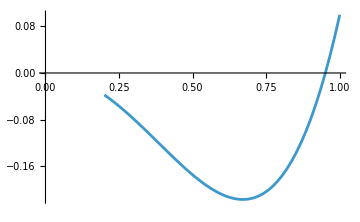

```mathematica
Plot[fz[t],{t,0.2,1},PlotRange->{{0,1},Automatic}]
```

```mathematica
SR1=RevolutionPlot3D[fz[t],{t,0.2,1}]
```

-Graphics3D-

```mathematica
(* Show the basic curve on the plot *)
```

```mathematica
f3z[t_]:={0,t,fz[t]}
```

```mathematica
CR1=ParametricPlot3D[f3z[t],{t,0.2,1},PlotStyle->{Purple,Thickness[0.025]}]
```

-Graphics3D-

```mathematica
(* Show the basic curve f3z[t] on the surface *)
```

```mathematica
Show[SR1,CR1]
```

-Graphics3D-

```mathematica
(* Show the plane x=0 *)
```

```mathematica
Clear[PlaneX0]
```

```mathematica
PlaneX0[x_,z_]:={0,x,z}
```

```mathematica
GPX0=ParametricPlot3D[PlaneX0[x,z],{x,-1,1},{z,-2,2},PlotStyle->{Gray,Opacity[0.7]},Mesh->None]
```

-Graphics3D-

```mathematica
Show[{SR1,CR1,GPX0}, ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* Self study: additional examples of pure functions *)
```

```mathematica
f0P:=Sin[#1^2]&
```

```mathematica
(* Call, graph: *)
```

```mathematica
f0P[3.]
```

0.412118

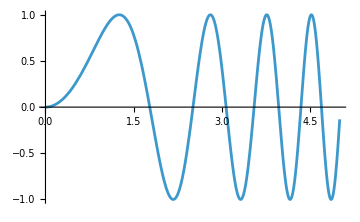

```mathematica
Plot[f0P[t],{t,0,5}]
```

```mathematica
(* Example 1P. f1L:R1->R2. Parametric function *)
```

```mathematica
R:=1
```

```mathematica
f1P={R Cos[#1],R/2Sin[#1]}&
```

{R Cos[#1],1/2 R Sin[#1]}&

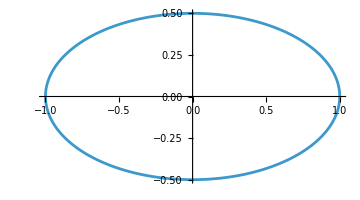

```mathematica
Pellipsoid=ParametricPlot[f1P[t],{t,0,2Pi}]
```

```mathematica
(* Example 2P. f1:R2->R1 *)
```

```mathematica
f12P:=Sin[#1^2]+Log[#1^2] Sin[#2^2]&
```

```mathematica
(* Call, graph: *)
```

```mathematica
f12P[0.1,2]
```

3.4952

```mathematica
P1=Plot3D[f12P[x,y],{x,0.1,5},{y,0,3}]
```

-Graphics3D-